```mathematica
(********************************************************************************************************
Copyright (c) 2013, Duncan J. Wingham, 
 Center for Polar Observation and Modelling,
 University College London, London, U.K.

Permission is hereby granted,free of charge,to any person obtaining a copy
of this software and associated documentation files (the "Software"),to deal
in the Software without restriction,including without limitation the rights
to use,copy,modify,merge,publish,distribute,sublicense,and/or sell
copies of the Software,and to permit persons to whom the Software is
furnished to do so,subject to the following conditions:

The above copyright notice and this permission notice shall be included in
all copies or substantial portions of the Software.

THE SOFTWARE IS PROVIDED "AS IS",WITHOUT WARRANTY OF ANY KIND,EXPRESS OR 
IMPLIED,INCLUDING BUT NOT LIMITED TO THE WARRANTIES OF MERCHANTABILITY,
 FITNESS FOR A PARTICULAR PURPOSE AND NONINFRINGEMENT.IN NO EVENT SHALL THE 
AUTHORS OR COPYRIGHT HOLDERS BE LIABLE FOR ANY CLAIM,DAMAGES OR OTHER
LIABILITY,WHETHER IN AN ACTION OF CONTRACT,TORT OR OTHERWISE,ARISING FROM,
 OUT OF OR IN CONNECTION WITH THE SOFTWARE OR THE USE OR OTHER DEALINGS IN
THE SOFTWARE.
*********************************************************************************************************)
```

{2013,11,1,12,30,55.244523}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{0.,InterpolatingFunction[{{-5.×10^-8,1.8×10^-7}},<>]}}

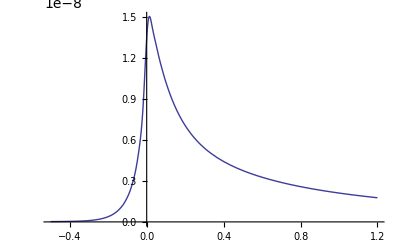

{2013,11,1,13,20,52.701762}

Set::write: Tag Times in .08\ (-π) is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Set::write: Tag Times in -1.47401\ .08 is Protected.

Set::write: Tag Times in -1.14295\ .08 is Protected.

Set::write: Tag Times in -1.01022\ .08 is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Set::write: Tag Times in .08\ (-π) is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

{{0.,InterpolatingFunction[{{-5.×10^-8,1.8×10^-7}},<>]}}

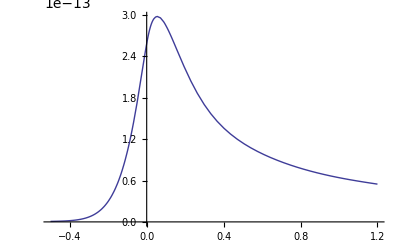

{2013,11,1,13,59,11.31816}

Set::write: Tag Times in .08\ (-π) is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Set::write: Tag Times in -1.47401\ .08 is Protected.

Set::write: Tag Times in -1.14295\ .08 is Protected.

Set::write: Tag Times in -1.01022\ .08 is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Set::write: Tag Times in .08\ (-π) is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

{{0.,InterpolatingFunction[{{-5.×10^-8,1.8×10^-7}},<>]}}

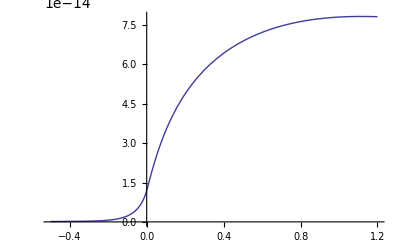

{2013,11,1,14,37,25.398204}

Set::write: Tag Times in .08\ (-π) is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Set::write: Tag Times in -1.47006\ .08 is Protected.

Set::write: Tag Times in -1.14212\ .08 is Protected.

Set::write: Tag Times in -1.00992\ .08 is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

Set::write: Tag Times in .08\ (-π) is Protected.

General::stop: Further output of Set :: write will be suppressed during this calculation.

{{0.,InterpolatingFunction[{{-5.×10^-8,1.8×10^-7}},<>]}}

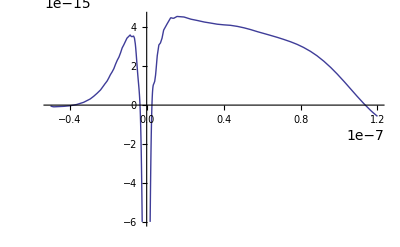

```mathematica
(* Description:
This code computes the CryoSat-2 pulse-limited (PL), SAR and SARin echoes. No input from the user is
required. Output files of the calculated model are generated and written by this script. A usage example, 
which plots examples of the model output waveforms, is provided below.

Please do familiarise yourself with the code, as certain segments of this code should be 
modified depending of which echo (PL, SAR or SARin) you would like to generate. 

A detailed description of the theory on which this code is built: 
"Precise Estimates of Ocean Surface Parameters from the CryoSat-2 Synthetic Aperture, Interferometric
Altimeter", Katharine A. Giles, Duncan J. Wingham, Natalia Galin, Robert Cullen, Walter H. F. Smith.

This code consists of two parts:
Part1) Code to generate and write to disk the look-up tables for PL, SAR and SARin echoes.
   Part2) Code to ingest the look-up tables generated in Part1, and demonstrate the use of these look-up tables, providing example plots of SAR and PL echoes. 

This code, the companion paper, and look-up tables (for SAR and PL modes) are available on the GitHub repository:
https://github.com/ngalin/CryoSat2_NumericalEchoModel

*)


(*******************************************************************************************************)
(*!!!!!!!!!BY DEFAULT THE ROUTINE CALCULATES CRYOSAT-2 SAR MODE ECHOES!!!!!!!!!!*)
(*******************************************************************************************************)

Clear[c,t,h,eta,r,k0,lambda,del,d,zeta,d0,thetaint,thetastart,theta,thetaw,kinc]

ns=10^(-9);
c=2.99792458 10^8;
(* h IS THE REFERENCE SATELLITE ALTITUDE IN METRES *)
h=720000;
(* r IS THE REFERENCE EARTH RADIUS IN METRES *)
r=6380000;
eta=1+h/r;
(* lambda IS THE CARRIER WAVELENGTH IN METRES *)
lambda=c/( 13.575 10^9);
k0=2 Pi/lambda;
(* del IS THE SPACING OF THE SAMPLES IN THE SYNTHETIC APERTURE *)
del=7200./18182;

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* zeta IS THE ANGULAR WIDTH OF A SYNTHETIC BEAM. SEE NOTE CONCERNING NUMBER OF BEAMS BELOW. *)
zeta=Pi/(64 k0 del);
(*In PL mode, set zeta = 0*)
(*zeta = 0*)
(* d0 IS THE SYNTHETIC BEAM GAIN. d0=4096 IS FOR A RECTANGULAR WEIGHTING ON THE SYNTHETIC APERTURE; IF USING A HAMMING WEIGHTING (SEE BELOW) use d0=1162.8100000000006 INSTEAD. *)
(*d0=4096*)
d0 = 1162.8100000000006; (*SAR Hamming window*)
(*In PL mode, set d0 = 1*)
(*d0 = 1*)
(***********************************************************************)

(* bandwidth IS THE COMPRESSED PULSE BANDWIDTH *)
bandwidth=320000000.;
(* res IS THE SAMPLING INTERVAL IN DELAY TIME OF THE ECHOES *)
res=1/bandwidth;

gammabar=0.012215368000378016;
gammahat=0.0381925958945466;
gamma1=Sqrt[2/(2/gammabar^2+2/gammahat^2)];
gamma2=Sqrt[2/(2/gammabar^2-2/gammahat^2)];

beta=Pi/2;

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* THE NEXT LINE SETS THE BASELINE. IF THIS PARAMETER IS NON-ZERO, THE CODE WILL EVALUATE THE INTEFEROMETRIC CROSS PRODUCT. IF YOU SET THIS PARAMETER TO ZERO, IT WILL EVALUATE THE SARIN OR SAR ECHO POWER. *)
 (*In PL mode, set baseline = 0;*)
baseline=0;(*1.1676;*)
(***********************************************************************)

(* THIS NEXT SUBROUTINE IS THE ANTENNA GAIN PATTERN *)
gainsqr[roe_,thetaw_]:=Exp[-2( ((roe Cos[thetaw])/gamma1)^2+((roe Sin[thetaw])/gamma2)^2)]

(* THIS NEXT SUBROUTINE IS THE COMPRESSED PULSE SHAPE *)
pulse[t_]:=If[t==0,1,(Sin[Pi t/res]/(Pi t/res))^2]

(* THIS NEXT SUBROUTINE IS THE SURFACE ROUGHNESS DISTRIBUTION *)
rough0[t_,sigma_]:=1/(Sqrt[2 Pi] sigma) Exp[-(1/2) (t/sigma)^2]

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* THIS NEXT CODE SPECIFIES RECTANGULAR WEIGHTING ON THE SYNTHETIC APERTURE  *)
(*d[theta_]:=(1/4096)(Cos[109.82593388049635 theta]+Cos[329.47780164148907 theta]+Cos[549.1296694024817 theta]+Cos[768.7815371634745 theta]+Cos[988.433404924467 theta]+Cos[1208.0852726854598 theta]+Cos[1427.7371404464525 theta]+Cos[1647.3890082074452 theta]+Cos[1867.040875968438 theta]+Cos[2086.6927437294307 theta]+Cos[2306.344611490423 theta]+Cos[2525.996479251416 theta]+Cos[2745.6483470124085 theta]+Cos[2965.3002147734014 theta]+Cos[3184.9520825343943 theta]+Cos[3404.6039502953868 theta]+Cos[3624.2558180563797 theta]+Cos[3843.9076858173717 theta]+Cos[4063.5595535783646 theta]+Cos[4283.211421339358 theta]+Cos[4502.86328910035 theta]+Cos[4722.515156861343 theta]+Cos[4942.167024622336 theta]+Cos[5161.818892383329 theta]+Cos[5381.470760144321 theta]+Cos[5601.1226279053135 theta]+Cos[5820.774495666306 theta]+Cos[6040.426363427299 theta]+Cos[6260.078231188292 theta]+Cos[6479.730098949284 theta]+Cos[6699.381966710277 theta]+Cos[6919.03383447127 theta])^2;*)

(*  IF YOU WANT HAMMING WEIGHTING ON THE SYNTHETIC APERTURE, USE THIS CODE INSTEAD.*)
d[theta_]:=(1/1162.8100000000006)(1.9988563675214088 Cos[109.82593388049635 theta]+1.9897243601271184 Cos[329.47780164148907 theta]+1.9715511033307518 Cos[549.1296694024817 theta]+1.9445172111230358 Cos[768.7815371634745 theta]+1.9088913584702256 Cos[988.433404924467 theta]+1.8650276111015833 Cos[1208.0852726854598 theta]+1.8133619066450888 Cos[1427.7371404464525 theta]+1.7544077220834402 Cos[1647.3890082074452 theta]+1.6887509705891108 Cos[1867.040875968438 theta]+1.6170441784560068 Cos[2086.6927437294307 theta]+1.5400000000000003 Cos[2306.344611490423 theta]+1.4583841348801627 Cos[2525.996479251416 theta]+1.37300771823155 Cos[2745.6483470124085 theta]+1.2847192592398093 Cos[2965.3002147734014 theta]+1.1943962082756865 Cos[3184.9520825343943 theta]+1.1029362363990272 Cos[3404.6039502953868 theta]+1.0112483139004902 Cos[3624.2558180563797 theta]+0.9202436765464241 Cos[3843.9076858173717 theta]+0.8308267693084356 Cos[4063.5595535783646 theta]+0.7438862575829166 Cos[4283.211421339358 theta]+0.6602861952350905 Cos[4502.86328910035 theta]+0.5808574372435015 Cos[4722.515156861343 theta]+0.5063893822899657 Cos[4942.167024622336 theta]+0.4376221273608131 Cos[5161.818892383329 theta]+0.3752391123305404 Cos[5381.470760144321 theta]+0.31986032762928496 Cos[5601.1226279053135 theta]+0.27203615249938984 Cos[5820.774495666306 theta]+0.23224188507922494 Cos[6040.426363427299 theta]+0.20087301867675067 Cos[6260.078231188292 theta]+0.17824131117933972 Cos[6479.730098949284 theta]+0.1645716866638307 Cos[6699.381966710277 theta]+0.16000000000000003 Cos[6919.03383447127 theta])^2 ;

(* WHEN GENERATING PL ECHOES SET: d[theta_]:= 1 *)
(*d[theta_]:=1*)
(***********************************************************************)


(* THE TOTAL NUMBER OF BEAMS IS 2 knrange + 1. THIS CODE HAS BEEN SET UP TO DEAL WITH THE AZIMUTHAL FFT OF A BURST, WHICH HAS 63 BEAMS. AS THIS CODE IS SET UP, IT ASSUMES THAT THERE IS AS MANY FORWARD BEAMS AS BACKWARD ONES. NOTE THAT IF YOU WISH TO APPLY TO A STACK, WHICH IN SAR MODE HAS MORE BEAMS, YOU WILL NEED TO ALTER NOT JUST THE NUMBER OF BEAMS, BUT ALSO ACCOUNT FOR THE FACT THAT THE ANGULAR SAMPLING OF A STACK IS NOT EQUAL TO THE ANGULAR WIDTH OF A BEAM. HOWEVER IN PRACTICE, THE ANGULAR BEHAVIOUR IS HIGHLY SAMPLED EVEN WITH 63 BEAMS. INCREASING THE NUMBER OF BEAMS DOES NOT IN PRACTICE ALTER THE SHAPE OF THE MULTI-LOOKED ECHO, SIMPLY ITS POWER. IF YOU WISH TO APPLY TO STACKS, YOU NEED SIMPLY TO MULTIPLY THE POWER BY THE RATIO OF THE NUMBER OF BEAMS IN THE STACK TO THE NUMBER IN THIS CALCULATION (63 AS IT IS PRESENTLY SET UP.) *)
knrange=31;
(* THE IMPULSE RESPONSE VARIES VERY RAPIDLY WHEN THE BEAM IS NEAR NORMAL INCIDENCE. IN THE CODE BELOW, THE NUMERICAL INTEGRATION OF THESE BEAMS IS DONE FOR A HIGHER SAMPLING RATE THAN THE OTHER BEAMS. knmid SPECIFIES THE NUMBER OF BEAMS AROUND THE NADIR BEAM FOR WHICH THIS HIGHER SAMPLING INTERVAL IS USED. *)
knmid=3;

(* istart SPECIFIES THE EARLIEST DELAY TIME IN ns FOR WHICH THE IMPULSE RESPONSE IS EVALUATED *)
istart=-50;
(* iend  SPECIFIES THE LATEST DELAY TIME IN ns FOR WHICH THE IMPULSE RESPONSE IS EVALUATED *)
iend=180;

zetab=500/h;

npoints=(iend-istart)/0.1;

(* nsigma SPECIFIES THE NUMBER OF VALUES OF SURFACE ROUGHNESS IN THE LOOK UP TABLES *)
nsigma=25;
(* sigmaint SPECIFIES THE SAMPLING INTERVAL IN METRES OF THE SURFACE ROUGHNESS STANDARD DEVIATION OF THE LOOK UP TABLES. *)
sigmaint=0.10;

(* WHAT FOLLOWS NOW ARE FOUR BLOCKS OF CODE THAT ARE ESSENTIALLY SIMILAR, AND WHICH ARE SEPARATED BY THE WRITING OF A LOOK UP TABLE TO DISC. THESE FOUR BLOCKS CORRESPOND TO THE TERMS IN THE SERIES REPRESENTATION THAT GIVES AS PERTURBATIONS THE EFFECT OF PITCH, ROLL AND HEIGHT RESPECTIVELY, WITH THE FIRST BLOCK PROVIDING THE UNPERTURBED LOOK UP TABLES. IN WHAT FOLLOWS, ONLY THE FIRST BLOCK IS COMMENTED; IN THE REMAINING BLOCKS, ONLY DIFFERENCES ARE IDENTIFIED.

NOTE THAT THIS CODE ASSUMES THAT PITCH AND ROLL ARE SMALL. IF YOU WANT THE RESULT FOR A LARGE PITCH OR ROLL, YOU WILL NEED TO INCLUDE THEIR EFFECT DIRECTLY IN THE DEFINITION OF THE ANTENNA GAIN PATTERN gainsqr ABOVE. IN THAT CASE, HOWEVER, YOU ONLY NEED TO RUN THE FIRST BLOCK OF CODE BELOW. *)

DateList[]

(* icre EQUALS THE SAMPLING INTERVAL IN ns WITH WHICH THE IMPULSE RESPONSE IS SAMPLED *)

icre=1.0;

(* WITHIN THIS BLOCK, THERE ARE THREE REPEATED SUB-BLOCKS OF INTEGRATION, IDENTIFIABLE BY THE CALL TO Monitor. THE FIRST SET DOES THE BACKWARD LOOKING BEAMS, THE SECOND THE FORWARD LOOKING BEAMS, THE THIRD SET THE CENTRAL BEAMS. *)

(* THE CALL TO Monitor INDICATES THE CALCULATION OF THE IMPULSE RESPONSE AT SUCCESSIVE INSTANTS OF ECHO DELAY TIME tor. THE INTEGRATION IS PERFORMED AROUND A RANGE RING. WHEN tor IS SMALL, THE INTEGRAND OCCUPIES MOST OF THE DOMAIN, BUT WHEN tor IS LARGE, THE INTEGRAND IS EFFECTIVELY NON-ZERO ONLY FOR A SMALL PART OF THE DOMAIN. THUS MOST OF THE CODE IS CONCERNED WITH IDENTIFYING THAT PART OF THE DOMAIN FOR WHICH THE INTEGRAND IS EFFECTIVELY NON-ZERO. *)

Monitor[part1out1=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;
*)
(***********************************************************************)

(* AND NEXT IS THE ACTUAL INTEGRATION: thetaw IS THE INTEGRATION VARIABLE EQUAL TO AN ANGLE SPECIFYING THE POSITION ON THE RANGE RING. *)

(NIntegrate[gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+NIntegrate[gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,-knrange,-knmid},{i,istart,iend,icre}],{i,j}];

(* THIS SUMS OVER THE BEAMS *)
part1sum1=Table[{part1out1[[1,i,1]],Sum[part1out1[[j,i,2]],{j,1,knrange-knmid+1,1}]},{i,1,1+(iend-istart)/icre}];
part1f0=Interpolation[part1sum1];

Monitor[part3out1=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;
*)
(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(NIntegrate[gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+NIntegrate[gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,knmid,knrange},{i,istart,iend,icre}],{i,j}];

part3sum1=Table[{part3out1[[1,i,1]],Sum[part3out1[[j,i,2]],{j,1,knrange-knmid+1,1}]},{i,1,1+(iend-istart)/icre}];
part3f0=Interpolation[part3sum1];

icre=0.1;

Monitor[part2out1=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;
*)
(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(NIntegrate[gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+NIntegrate[gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,-knmid+1,knmid-1},{i,istart,iend,icre}],{i,j}];

part2sum1=Table[{part2out1[[1,i,1]],Sum[part2out1[[j,i,2]],{j,1,2(knmid-1)+1,1}]},{i,1,1+(iend-istart)/icre}];
part2f0=Interpolation[part2sum1];

(* THE NEXT LINE SUMS THE THREE SETS OF BEAMS TOGETHER *)
samf0=Table[part1f0[istart ns+0.1 i ns]+part3f0[istart ns+0.1 i ns]+part2f0[istart ns+0.1 i ns],{i,0,npoints}];

(* THE NEXT BLOCK OF CODE DOES THE CONVOLUTION WITH THE COMPRESSED PULSE. IT USES FFT METHODS TO IMPLEMENMT THIS. *)

sampan=Table[If[i<2048,pulse[0.1 (i-1) ns],pulse[0.1 (i-4197) ns]],{i,1,4196}];
zeroes=Table[0.,{i,npoints+2,4196}];
samf0extend=Join[samf0,zeroes];
trsamf0extend=Sqrt[4196]10^(-10)Fourier[samf0extend,FourierParameters->{0,1}];
trsampan=Sqrt[4196]10^(-10)Fourier[sampan,FourierParameters->{0,1}];
prod=Table[trsampan[[i]] trsamf0extend[[i]],{i,1,4196}];
conv=(1/Sqrt[4196])(1/10^(-10))Fourier[prod,FourierParameters->{0,-1}];
pwr=Table[{istart ns +0.1 i ns,conv[[i+1]]},{i,0,npoints}];
g01=Interpolation[pwr];  


(* THE NEXT BLOCK OF CODE DOES THE CONVOLUTION OVER THE SURFACE ROUGHNESS DISTRIBUTION, FOR A SEQUENCE OF VALUES OF ROUGHNESS STANDARD DEVIATION. IT USES FFT METHODS TO IMPLEMENT THIS *)

zerosig={{0.,g01}}
echoes=Table[{sigma=(2/c) sigmaint j,samf0=Table[g01[istart ns+0.1 i ns],{i,0,npoints}];
sampan1=Table[If[i<2048,rough0[0.1 (i-1) ns,sigma],rough0[0.1 (i-4197) ns,sigma]],{i,1,4196}];
zeroes=Table[0.,{i,npoints+2,4196}];
samf0extend=Join[samf0,zeroes];
trsamf0extend=Sqrt[4196]10^(-10)Fourier[samf0extend,FourierParameters->{0,1}];
trsampan=Sqrt[4196]10^(-10)Fourier[sampan1,FourierParameters->{0,1}];
prod=Table[trsampan[[i]] trsamf0extend[[i]],{i,1,4196}];
conv=(1/Sqrt[4196])(1/10^(-10))Fourier[prod,FourierParameters->{0,-1}];
pwr=Table[{istart ns +0.1 i ns,conv[[i]]},{i,0,npoints}];
g1=Interpolation[pwr]},{j,1,nsigma}];

(*FOR ZERO WAVEHEIGHT,THE ROUGHNESS DISTRIBUTION IS A DELTA FUNCTION. THE NEXT LINE APPENDS TO THE FRONT OF THE LOOK-UP TABLE, THE ZERO WAVEHEIGHT RESULT*)
echoes0=Join[zerosig,echoes];
Plot[echoes0[[1,2]][t],{t,-50 ns,120 ns}]  

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* THE NEXT LINE WRITES TO DISK THE NUMERICAL PART OF THE MODEL AS A LOOK UP TABLE WITH ENTRIES FOR SUCCESSIVE VALUES OF ROUGHNESS AND DELAY TIME *)
(* Depending on mode, change the filename appropriately: *)
 (*echoes0>>"SAR Rectangular 63 beams h0"*) (*SAR mode filename*)
(*echoes0>>"PL h0" (*PL mode filename*)*)
echoes0>>"SAR Hamming 63 beams h0"
(***********************************************************************)

DateList[]

(* THIS NEXT BLOCK CALCULATES THE cos^2 TERM IN THE PERTURBATIONS FOR PITCH AND ROLL  *)

icre=1.0;

Monitor[part1out2=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(roe^2 NIntegrate[Cos[thetaw]^2 gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+roe^2 NIntegrate[Cos[thetaw]^2gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,-knrange,-knmid},{i,istart,iend,icre}],{i,j}];

part1sum21=Table[{part1out2[[1,i,1]],Sum[part1out2[[j,i,2]],{j,1,knrange-knmid+1,1}]},{i,1,1+(iend-istart)/icre}];
part1f21=Interpolation[part1sum21];

Monitor[part3out2=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(roe^2 NIntegrate[Cos[thetaw]^2 gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak]Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])] ,{thetaw,lowerlimitminus,lowerlimitplus}]+roe^2 NIntegrate[Cos[thetaw]^2gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,knmid,knrange},{i,istart,iend,icre}],{i,j}];

part3sum21=Table[{part3out2[[1,i,1]],Sum[part3out2[[j,i,2]],{j,1,knrange-knmid+1,1}]},{i,1,1+(iend-istart)/icre}];
part3f21=Interpolation[part3sum21];

icre=0.1;

Monitor[part2out21=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(roe^2 NIntegrate[Cos[thetaw]^2 gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+roe^2 NIntegrate[Cos[thetaw]^2gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,-knmid+1,knmid-1},{i,istart,iend,icre}],{i,j}];

part2sum21=Table[{part2out21[[1,i,1]],Sum[part2out21[[j,i,2]],{j,1,2(knmid-1)+1,1}]},{i,1,1+(iend-istart)/icre}];
part2f21=Interpolation[part2sum21];

samf0=Table[part1f21[istart ns+0.1 i ns]+part3f21[istart ns+0.1 i ns]+part2f21[istart ns+0.1 i ns],{i,0,npoints}];

sampan=Table[If[i<2048,pulse[0.1 (i-1) ns],pulse[0.1 (i-4197) ns]],{i,1,4196}];
zeroes=Table[0.,{i,npoints+2,4196}];
samf0extend=Join[samf0,zeroes];
trsamf0extend=Sqrt[4196]10^(-10)Fourier[samf0extend,FourierParameters->{0,1}];
trsampan=Sqrt[4196]10^(-10)Fourier[sampan,FourierParameters->{0,1}];
prod=Table[trsampan[[i]] trsamf0extend[[i]],{i,1,4196}];
conv=(1/Sqrt[4196])(1/10^(-10))Fourier[prod,FourierParameters->{0,-1}];
pwr=Table[{istart ns +0.1 i ns,conv[[i+1]]},{i,0,npoints}];
g11=Interpolation[pwr];

zerosig={{0.,g11}}
echoes=Table[{sigma=(2/c) sigmaint j,samf0=Table[g11[istart ns+0.1 i ns],{i,0,npoints}];
sampan1=Table[If[i<2048,rough0[0.1 (i-1) ns,sigma],rough0[0.1 (i-4197) ns,sigma]],{i,1,4196}];
zeroes=Table[0.,{i,npoints+2,4196}];
samf0extend=Join[samf0,zeroes];
trsamf0extend=Sqrt[4196]10^(-10)Fourier[samf0extend,FourierParameters->{0,1}];
trsampan=Sqrt[4196]10^(-10)Fourier[sampan1,FourierParameters->{0,1}];
prod=Table[trsampan[[i]] trsamf0extend[[i]],{i,1,4196}];
conv=(1/Sqrt[4196])(1/10^(-10))Fourier[prod,FourierParameters->{0,-1}];
pwr=Table[{istart ns +0.1 i ns,conv[[i]]},{i,0,npoints}];
g1=Interpolation[pwr]},{j,1,nsigma}];

echoes1=Join[zerosig,echoes];
Plot[echoes1[[1,2]][t],{t,-50 ns,120 ns}]  

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* THE NEXT LINE WRITES TO DISK THE NUMERICAL PART OF THE MODEL AS A LOOK UP TABLE WITH ENTRIES FOR SUCCESSIVE VALUES OF ROUGHNESS AND DELAY TIME *)
(* Depending on mode, change the filename appropriately: *)
(*echoes1 >>"SAR Rectangular 63 beams h11"*)(*SAR mode filename*)
(*echoes1>>"PL h11"(*PL mode filename*)*)
echoes1>>"SAR Hamming 63 beams h11"
 (***********************************************************************)

DateList[]

(* THIS NEXT BLOCK DOES THE sin^2 PERTURBATION *)

icre=1.0;

Monitor[part1out3=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(roe^2 NIntegrate[Sin[thetaw]^2 gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+roe^2 NIntegrate[Sin[thetaw]^2gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,-knrange,-knmid},{i,istart,iend,icre}],{i,j}];

part1sum31=Table[{part1out3[[1,i,1]],Sum[part1out3[[j,i,2]],{j,1,knrange-knmid+1,1}]},{i,1,1+(iend-istart)/icre}];
part1f22=Interpolation[part1sum31];

Monitor[part3out3=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(roe^2 NIntegrate[Sin[thetaw]^2 gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+roe^2 NIntegrate[Sin[thetaw]^2gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,knmid,knrange},{i,istart,iend,icre}],{i,j}];

part3sum22=Table[{part3out3[[1,i,1]],Sum[part3out3[[j,i,2]],{j,1,knrange-knmid+1,1}]},{i,1,1+(iend-istart)/icre}];
part3f22=Interpolation[part3sum22];

icre=0.1;

Monitor[part2out22=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/(h eta)+zetak^2<0,0,
roe=Sqrt[c tor/(h eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(roe^2 NIntegrate[Sin[thetaw]^2 gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+roe^2 NIntegrate[Sin[thetaw]^2gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,-knmid+1,knmid-1},{i,istart,iend,icre}],{i,j}];

part2sum22=Table[{part2out22[[1,i,1]],Sum[part2out22[[j,i,2]],{j,1,2(knmid-1)+1,1}]},{i,1,1+(iend-istart)/icre}];
part2f22=Interpolation[part2sum22];

samf0=Table[part1f22[istart ns+0.1 i ns]+part3f22[istart ns+0.1 i ns]+part2f22[istart ns+0.1 i ns],{i,0,npoints}];
sampan=Table[If[i<2048,pulse[0.1 (i-1) ns],pulse[0.1 (i-4197) ns]],{i,1,4196}];
zeroes=Table[0.,{i,npoints+2,4196}];
samf0extend=Join[samf0,zeroes];
trsamf0extend=Sqrt[4196]10^(-10)Fourier[samf0extend,FourierParameters->{0,1}];
trsampan=Sqrt[4196]10^(-10)Fourier[sampan,FourierParameters->{0,1}];
prod=Table[trsampan[[i]] trsamf0extend[[i]],{i,1,4196}];
conv=(1/Sqrt[4196])(1/10^(-10))Fourier[prod,FourierParameters->{0,-1}];

pwr=Table[{istart ns +0.1 i ns,conv[[i+1]]},{i,0,npoints}];
g12=Interpolation[pwr];


 
zerosig={{0.,g12}}
echoes=Table[{sigma=(2/c) sigmaint j,samf0=Table[g12[istart ns+0.1 i ns],{i,0,npoints}];
sampan1=Table[If[i<2048,rough0[0.1 (i-1) ns,sigma],rough0[0.1 (i-4197) ns,sigma]],{i,1,4196}];
zeroes=Table[0.,{i,npoints+2,4196}];
samf0extend=Join[samf0,zeroes];
trsamf0extend=Sqrt[4196]10^(-10)Fourier[samf0extend,FourierParameters->{0,1}];
trsampan=Sqrt[4196]10^(-10)Fourier[sampan1,FourierParameters->{0,1}];
prod=Table[trsampan[[i]] trsamf0extend[[i]],{i,1,4196}];
conv=(1/Sqrt[4196])(1/10^(-10))Fourier[prod,FourierParameters->{0,-1}];
pwr=Table[{istart ns +0.1 i ns,conv[[i]]},{i,0,npoints}];
g1=Interpolation[pwr]},{j,1,nsigma}];

echoes2=Join[zerosig,echoes];
Plot[echoes2[[1,2]][t],{t,-50 ns,120 ns}]

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* THE NEXT LINE WRITES TO DISK THE NUMERICAL PART OF THE MODEL AS A LOOK UP TABLE WITH ENTRIES FOR SUCCESSIVE VALUES OF ROUGHNESS AND DELAY TIME *)
(* Depending on mode, change the filename appropriately: *)
(*echoes2>> "SAR Rectangular 63 beams h12"*)(*SAR mode filename*)
(*echoes2>>"PL h12"(*PL mode filename*)*)
echoes2>>"SAR Hamming 63 beams h12"
 (***********************************************************************)

DateList[]

(* THIS FINAL BLOCK DOES THE PERTURBATION FOR ALTITUDE VARIATIONS. *)

delh=1000;
eta=1+(h+delh)/r;

icre=1.0;

Monitor[part1out4=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/((h+delh) eta)+zetak^2<0,0,
roe=Sqrt[c tor/((h+delh) eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(NIntegrate[gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+NIntegrate[gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,-knrange,-knmid},{i,istart,iend,icre}],{i,j}];

part1sum4=Table[{part1out4[[1,i,1]],Sum[part1out4[[j,i,2]],{j,1,knrange-knmid+1,1}]},{i,1,1+(iend-istart)/icre}];
part1f4=Interpolation[part1sum4];

Monitor[part3out4=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/((h+delh) eta)+zetak^2<0,0,
roe=Sqrt[c tor/((h+delh) eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)

(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(NIntegrate[gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak] Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])],{thetaw,lowerlimitminus,lowerlimitplus}]+NIntegrate[gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak]Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])] ,{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,knmid,knrange},{i,istart,iend,icre}],{i,j}];

part3sum4=Table[{part3out4[[1,i,1]],Sum[part3out4[[j,i,2]],{j,1,knrange-knmid+1,1}]},{i,1,1+(iend-istart)/icre}];
part3f4=Interpolation[part3sum4];

icre=0.1;

Monitor[part2out4=Table[{i 10.^(-9),tor=i*10.^(-9);zetak=j*zeta;If[c tor/((h+delh) eta)+zetak^2<0,0,
roe=Sqrt[c tor/((h+delh) eta)+zetak^2];
If[roe==0,width=2 Pi,width=1.2 Sqrt[zetab /roe]]
If[roe==0,ratio=10,ratio=zetak/roe]
If[roe==0,theta0=0,theta0=ArcCos[zetak/roe]]
If[ratio≥1,lowerlimitplus=0;lowerlimitminus=-width;upperlimitminus=0;upperlimitplus=width];
If[ratio≤-1,upperlimitplus=Pi;upperlimitminus=-Pi+width;lowerlimitminus=-Pi;lowerlimitplus=Pi-width];
If[ratio<1 && ratio≥0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[ratio>-1 && ratio<0,lowerlimitplus=theta0-width;lowerlimitminus=-theta0-width;upperlimitminus=-theta0+width;upperlimitplus=theta0+width];
If[lowerlimitminus<-Pi,lowerlimitminus=-Pi];
If[upperlimitminus>0,upperlimitminus=0];
If[lowerlimitplus<0,lowerlimitplus=0];
If[upperlimitplus>Pi,upperlimitplus=Pi];

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* In PL mode set these to: *)
(*NG*)
  lowerlimitplus = 0;
  upperlimitplus = Pi;.08
lowerlimitminus = -Pi;
  upperlimitminus = 0;

(***********************************************************************)
(* Plot[{d[roe Cos[theta]-zetak],g[theta]},{theta,-Pi,Pi},PlotRange->{0,1}]*)

(NIntegrate[gainsqr[roe,thetaw] d[roe Cos[thetaw]-zetak]Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])] ,{thetaw,lowerlimitminus,lowerlimitplus}]+NIntegrate[gainsqr[roe,thetaw]  d[roe Cos[thetaw]-zetak]Exp[I k0 baseline (roe Cos[thetaw-Pi/2]-Sin[theta])] ,{thetaw,upperlimitminus,upperlimitplus}] )/(2 Pi)]},{j,-knmid+1,knmid-1},{i,istart,iend,icre}],{i,j}];

part2sum4=Table[{part2out4[[1,i,1]],Sum[part2out4[[j,i,2]],{j,1,2(knmid-1)+1,1}]},{i,1,1+(iend-istart)/icre}];
part2f4=Interpolation[part2sum4];

samf0=Table[part1f4[istart ns+0.1 i ns]+part3f4[istart ns+0.1 i ns]+part2f4[istart ns+0.1 i ns],{i,0,npoints}];
sampan=Table[If[i<2048,pulse[0.1 (i-1) ns],pulse[0.1 (i-4197) ns]],{i,1,4196}];
zeroes=Table[0.,{i,npoints+2,4196}];
samf0extend=Join[samf0,zeroes];
trsamf0extend=Sqrt[4196]10^(-10)Fourier[samf0extend,FourierParameters->{0,1}];
trsampan=Sqrt[4196]10^(-10)Fourier[sampan,FourierParameters->{0,1}];
prod=Table[trsampan[[i]] trsamf0extend[[i]],{i,1,4196}];
conv=(1/Sqrt[4196])(1/10^(-10))Fourier[prod,FourierParameters->{0,-1}];
pwr=Table[{istart ns +0.1 i ns,conv[[i+1]]},{i,0,npoints}];
g03=Interpolation[pwr];

samf0=Table[(g03[istart ns+0.1 i ns]-g01[istart ns+0.1 i ns])/delh,{i,0,npoints}];
zero=Interpolation[Table[{istart ns +0.1 i ns,(g03[istart ns+0.1 i ns]-g01[istart ns+0.1 i ns])/delh},{i,0,npoints}]];

zerosig={{0.,zero}}
echoes=Table[{sigma=(2/c) sigmaint j,
sampan1=Table[If[i<2048,rough0[0.1 (i-1) ns,sigma],rough0[0.1 (i-4197) ns,sigma]],{i,1,4196}];
zeroes=Table[0.,{i,npoints+2,4196}];
samf0extend=Join[samf0,zeroes];
trsamf0extend=Sqrt[4196]10^(-10)Fourier[samf0extend,FourierParameters->{0,1}];
trsampan=Sqrt[4196]10^(-10)Fourier[sampan1,FourierParameters->{0,1}];
prod=Table[trsampan[[i]] trsamf0extend[[i]],{i,1,4196}];
conv=(1/Sqrt[4196])(1/10^(-10))Fourier[prod,FourierParameters->{0,-1}];
pwr=Table[{istart ns +0.1 i ns,conv[[i]]},{i,0,npoints}];
g1=Interpolation[pwr]},{j,1,nsigma}];

echoes3=Join[zerosig,echoes];
Plot[echoes3[[1,2]][t],{t,-50 ns,120 ns}]

(*WARNING: USER MODIFIABLE SEGMENT***************************************)
(* THE NEXT LINE WRITES TO DISK THE NUMERICAL PART OF THE MODEL AS A LOOK UP TABLE WITH ENTRIES FOR SUCCESSIVE VALUES OF ROUGHNESS AND DELAY TIME *)
(* Depending on mode, change the filename appropriately: *)
(*echoes3>>"SAR Rectangular 63 beams h2"*)(*SAR mode filename*)
(*echoes3>>"PL h2"(*PL mode filename*)*)
echoes3>>"SAR Hamming 63 beams h2"
 (***********************************************************************)
```

```mathematica
(* Description:
 THIS CODE PROVIDES THE MODEL OF THE SARIN, SAR AND PULSE-LIMITED ECHOES. NOTE THAT THE ACTUAL MODELS 
DEPEND ON THE LOOK UP TABLES THAT ARE READ IN AT THE START. THESE ARE NUMERICALLY CALCULATED USING
THE SAME VALUES OF THE CONSTANTS AS APPEAR IN THIS FILE. IF YOU CHANGE THE CONSTANTS IN THIS FILE,                WITHOUT HAVING RERUN THE INTEGRATION PROGRAM THAT GENERATES THE LOOK UP TABLES WITH THE SAME CHANGES,
 THE RESULTS WILL BE INCORRECT. IN A MORE USER FRIENDLY VERSION, THE CONSTANTS WOULD ALSO BE PASSED BY
FILE. I AGREE THAT THIS PRESENT WAY, ISN'T A VERY SECURE WAY TO DO THINGS. 
*)
```

{2013,11,1,16,29,25.623776}

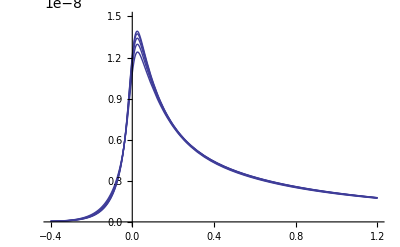

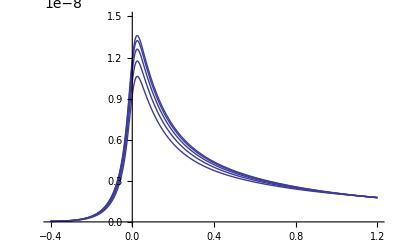

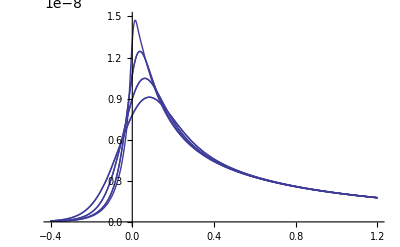

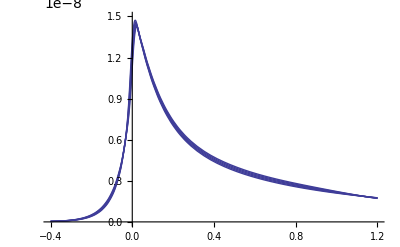

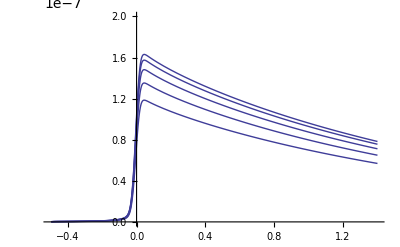

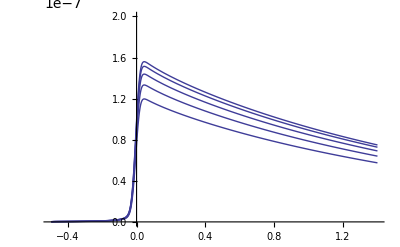

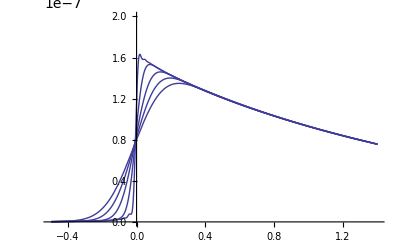

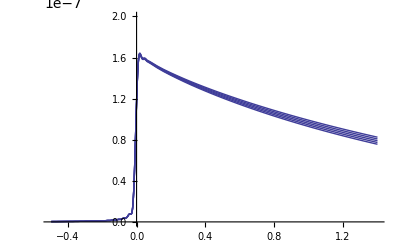

```mathematica
(*WARNING: USER MODIFIABLE SEGMENT***************************************) 
(*echoes0=<<"/Users/ngalin/Desktop/CryoSat2_NumericalEchoModel-master/SAR Rectangular 63 beams h0";
echoes1=<<"/Users/ngalin/Desktop/CryoSat2_NumericalEchoModel-master/SAR Rectangular 63 beams h11";
echoes2=<<"/Users/ngalin/Desktop/CryoSat2_NumericalEchoModel-master/SAR Rectangular 63 beams h12";
echoes3=<<"/Users/ngalin/Desktop/CryoSat2_NumericalEchoModel-master/SAR Rectangular 63 beams h2";*)

echoes0=<<"/Users/ngalin/SAR Hamming 63 beams h0";
echoes1=<<"/Users/ngalin/SAR Hamming 63 beams h11";
echoes2=<<"/Users/ngalin/SAR Hamming 63 beams h12";
echoes3=<<"/Users/ngalin/SAR Hamming 63 beams h2";

plechoes0=<<"/Users/ngalin/PL h0";
plechoes1 =<<"/Users/ngalin/PL h11";
plechoes2=<< "/Users/ngalin/PL h12";
plechoes3=<<"/Users/ngalin/PL h2";
 (***********************************************************************)

DateList[]
(* DO NOT CHANGE THE VALUE OF THESE CONSTANTS OR NAMES OF THESE FUNCTIONS. *)
ns=10^(-9);
istart=-50 ;
iend=140 ;
icre=0.1;
npoints=1+(iend-istart)/0.1;
nsigma=25;
lambda=c/( 13.575 10^9);
k0=2 Pi/lambda;
del=7200./18182;
zeta=Pi/(64 k0 del);
sigmaint=0.1;
ns=10^(-9);
c=2.99792458 10^8;
h=720000;
r=6380000;
gammabar=0.012215368000378016;
gammahat=0.0381925958945466;
gamma1=Sqrt[2/(2/gammabar^2+2/gammahat^2)];
gamma2=Sqrt[2/(2/gammabar^2-2/gammahat^2)];

h0approx=Interpolation[Flatten[Table[{{sigma=sigmaint (j-1),tor=(istart+(i-1)0.1) ns},echoes0[[j,2]][tor]},{j,1,nsigma+1},{i,1,npoints}],1]];

h11approx=Interpolation[Flatten[Table[{{sigma=sigmaint (j-1),tor=(istart+(i-1)0.1) ns},echoes1[[j,2]][tor]},{j,1,nsigma+1},{i,1,npoints}],1]];

h12approx=Interpolation[Flatten[Table[{{sigma=sigmaint (j-1),tor=(istart+(i-1)0.1) ns},echoes2[[j,2]][tor]},{j,1,nsigma+1},{i,1,npoints}],1]];

h2approx=Interpolation[Flatten[Table[{{sigma=sigmaint (j-1),tor=(istart+(i-1)0.1) ns},echoes3[[j,2]][tor]},{j,1,nsigma+1},{i,1,npoints}],1]];

sar51echoapproxv3[sigma_,tor_,pitch_,roll_,delh_]:=(1-2((pitch/gamma1)^2+(roll/gamma2)^2))h0approx[Sqrt[sigma^2],tor]+8 ((pitch^2/gamma1^4)h11approx[Sqrt[sigma^2],tor]+(roll^2/gamma2^4) h12approx[Sqrt[sigma^2],tor])+delh h2approx[Sqrt[sigma^2],tor]

f0approx=Interpolation[Flatten[Table[{{sigma=sigmaint (j-1),tor=(istart+(i-1)0.1) ns},plechoes0[[j,2]][tor]},{j,1,nsigma+1},{i,1,npoints}],1]];

f11approx=Interpolation[Flatten[Table[{{sigma=sigmaint (j-1),tor=(istart+(i-1)0.1) ns},plechoes1[[j,2]][tor]},{j,1,nsigma+1},{i,1,npoints}],1]];

f12approx=Interpolation[Flatten[Table[{{sigma=sigmaint (j-1),tor=(istart+(i-1)0.1) ns},plechoes2[[j,2]][tor]},{j,1,nsigma+1},{i,1,npoints}],1]];

f2approx=Interpolation[Flatten[Table[{{sigma=sigmaint (j-1),tor=(istart+(i-1)0.1) ns},plechoes3[[j,2]][tor]},{j,1,nsigma+1},{i,1,npoints}],1]];

plechoapproxv2[sigma_,tor_,pitch_,roll_,delh_]:=(1-2((pitch/gamma1)^2+(roll/gamma2)^2)) f0approx[sigma,tor]+8 (c tor/(h (1+h/r)))((pitch^2/gamma1^4)f11approx[sigma,tor]+(roll^2/gamma2^4) f12approx[sigma,tor])+delh f2approx[sigma,tor]

(* END OF CONSTANTS AND FUNCTIONS BLOCK  *) 

(* THIS CODE ILLSTRATES THE USE OF THE MODELS *)
pitch=0.1*Pi/180;
roll=0;
delh=0;
sigma=0.25;

(* SOME SAR MODE EXAMPLES *)
Plot[Table[sar51echoapproxv3[sigma, tor,0.05 i Pi/180,roll,delh],{i,1,5}],{tor,-40 ns, 120 ns},PlotRange->{0,1.5 10^(-8)}]
sarHam01 = Table[sar51echoapproxv3[sigma,tor,0.05i Pi/180,roll,delh],{i,1,1},{tor,-40ns,120ns,1.5625ns}];
Export["sarHam01.txt",sarHam01];

Plot[Table[sar51echoapproxv3[sigma, tor,pitch,0.05 i Pi/180,delh],{i,1,5}],{tor,-40 ns, 120 ns},PlotRange->{0,1.5 10^(-8)}]  
sarHam06 = Table[sar51echoapproxv3[sigma,tor,pitch,0.05i Pi/180,delh],{i,1,1},{tor,-40ns,120ns,1.5625ns}];
Export["sarHam06.txt",sarHam06];

Plot[Table[sar51echoapproxv3[0.5i, tor,pitch,roll,delh],{i,-3,3}],{tor,-40 ns, 120 ns},PlotRange->{0,1.5 10^(-8)}]
sarHam11 = Table[sar51echoapproxv3[0.5i,tor,pitch,roll,delh],{i,-3,-3},{tor,-40ns,120ns,1.5625ns}];
Export["sarHam11.txt",sarHam11];

Plot[Table[sar51echoapproxv3[0., tor,pitch,roll,(i-1) 20000],{i,1,5}],{tor,-40 ns, 120 ns},PlotRange->{0,1.5 10^(-8)}] 
sarHam16 = Table[sar51echoapproxv3[0.,tor,pitch,roll,(i-1)20000],{i,1,1},{tor,-40ns,120ns,1.5625ns}];
Export["sarHam16.txt",sarHam16];

 (* SOME PULSE-LIMITED EXAMPLES *)
Plot[Table[plechoapproxv2[sigma, tor,0.05 i Pi/180,roll,delh],{i,1,5}],{tor,-50 ns, 140 ns},PlotRange->{0,2.0 10^(-7)}]
Plot[Table[plechoapproxv2[sigma, tor,pitch,0.05 i Pi/180,delh],{i,1,5}],{tor,-50 ns, 140 ns},PlotRange->{0,2.0 10^(-7)}]
Plot[Table[plechoapproxv2[0.5(i-1), tor,pitch,roll,delh],{i,1,5}],{tor,-50 ns, 140 ns},PlotRange->{0,2.0 10^(-7)}]
Plot[Table[plechoapproxv2[0., tor,pitch,roll,(i-1) 20000],{i,1,5}],{tor,-50 ns, 140 ns},PlotRange->{0,2.0 10^(-7)}]
```